```mathematica
ϵ0[m_]=If[m==0, -s kappa, Sign[m]Sqrt[Abs[m]+ kappa^2]];
ϵdiv=tz kappa;
alpha[m_]=(-Sqrt[Abs[m]])/(ϵ0[m] s - kappa);
xi=((alpha[m]^2+1)(alpha[n]^2+1))^(-1)/(ϵ0[m]-ϵ0[n])^2; (*Nb defined without heaviside *)
```

```mathematica
Integrate[
xi (ϵ0[m] + ϵ0[n]) alpha[m]^2/.{n->0, m->1,s->1},
{kappa,  0, Infinity}
]
```

1/4

```mathematica
Table[
Integrate[
xi (ϵ0[m] + ϵ0[n]) alpha[m]^2/.{n->-i, m->i+1,s->1},
{kappa,  -Infinity, Infinity}
],
{i, 1,2}
]
```

```mathematica
FullSimplify[xi (ϵ0[m] + ϵ0[n]) alpha[m]^2/.s->1, {m>0, n<0, {m,n}∈Reals}]
```

(m (√(kappa^2+m)-√(kappa^2+Abs[n])) (kappa+√(kappa^2+Abs[n]))^2)/(4 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2+Abs[n]))^2 (Abs[n]+kappa (kappa+√(kappa^2+Abs[n]))))

```mathematica
FullSimplify[xi (tz kappa) alpha[n]^2/.s->1, {m>0, n<0, {m,n}∈Reals}]/.Abs[n]->-n
```

-((kappa (kappa-√(kappa^2+m))^2 n tz)/(4 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2-n))^2 (kappa (kappa+√(kappa^2-n))-n)))

```mathematica
Integrate[
%,
{kappa, -limit, limit},
Assumptions->{{m,n}∈Integers, m>0, n<0, tz∈Reals, 0<=tz<1, limit>0, limit ∈Reals}
]
```

-(tz (limit (-√(limit^2+m)+√(limit^2-n))+m ArcTanh[limit/(√(limit^2+m))]+n ArcTanh[limit/(√(limit^2-n))]))/(4 (m+n))

```mathematica
-(tz (limit (-√(limit^2+m)+√(limit^2-n))+m ArcTanh[limit/(√(limit^2+m))]+n ArcTanh[limit/(√(limit^2-n))]))/(4 (m+n))/.n->-m-1'
```

1/4 tz (limit (-√(limit^2+m)+√(1+limit^2+m))+m ArcTanh[limit/(√(limit^2+m))]+(-1-m) ArcTanh[limit/(√(1+limit^2+m))])

```mathematica
FullSimplify[%, Assumptions->{m∈PositiveIntegers, {tz, limit}∈Reals, 0<=tz<1, limit>0}]
```

-1/4 tz (limit (√(limit^2+m)-√(1+limit^2+m))-m ArcTanh[limit/(√(limit^2+m))]+(1+m) ArcTanh[limit/(√(1+limit^2+m))])

```mathematica
1/4 tz (limit (√(-1+limit^2+m)-√(limit^2+m))+(1-m) ArcTanh[limit/(√(-1+limit^2+m))]+m ArcTanh[limit/(√(limit^2+m))])//Simplify
```

1/4 tz (limit (√(-1+limit^2+m)-√(limit^2+m))-(-1+m) ArcTanh[limit/(√(-1+limit^2+m))]+m ArcTanh[limit/(√(limit^2+m))])

```mathematica
Table[(tz (limit (-√(limit^2+m)+√(limit^2-n))+m ArcTanh[limit/(√(limit^2+m))]+n ArcTanh[limit/(√(limit^2-n))]))/(4 (m+n))/.n->-m+1, {tz, {0,0.1}}]/.m->1
```

{0,0.025 (limit (√(limit^2)-√(1+limit^2))+ArcTanh[limit/(√(1+limit^2))])}

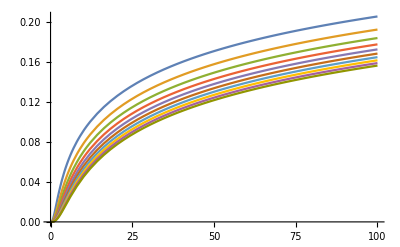

```mathematica
Plot[
Evaluate[Table[(tz (limit (-√(limit^2+m)+√(limit^2-n))+m ArcTanh[limit/(√(limit^2+m))]+n ArcTanh[limit/(√(limit^2-n))]))/(4 (m+n))/.n->-m-1, {m, 10}]/.tz->0.2],
{limit, 0,100}
]
```

```mathematica
Table[
Table[(tz (limit (-√(limit^2+m)+√(limit^2-n))+m ArcTanh[limit/(√(limit^2+m))]+n ArcTanh[limit/(√(limit^2-n))]))/(4 (m+n))/.n->-m-1, {m, 10}]/.tz->0.2,
{limit, 0,100}
]//Transpose
```

{{0,0.00588735,0.0210976,0.0355867,0.0476321,0.0576385,0.0661097,0.0734213,0.0798379,0.0855475,0.0906864,0.0953559,0.0996333,0.103578,0.107238,0.110651,0.113848,0.116855,0.119692,0.122377,0.124927,0.127353,0.129668,0.131881,0.134,0.136034,0.137988,0.139869,0.141682,0.143432,0.145122,0.146758,0.148342,0.149877,0.151367,0.152813,0.154219,0.155587,0.156918,0.158215,0.159479,0.160712,0.161915,0.16309,0.164239,0.165361,0.166459,0.167533,0.168584,0.169614,0.170624,0.171613,0.172583,0.173535,0.174468,0.175385,0.176286,0.17717,0.178039,0.178893,0.179733,0.180559,0.181371,0.182171,0.182958,0.183733,0.184496,0.185247,0.185988,0.186717,0.187436,0.188145,0.188844,0.189534,0.190214,0.190884,0.191546,0.1922,0.192845,0.193481,0.19411,0.194731,0.195344,0.19595,0.196549,0.19714,0.197725,0.198303,0.198874,0.199439,0.199997,0.20055,0.201096,0.201636,0.202171,0.2027,0.203224,0.203742,0.204254,0.204762,0.205264},{0,0.00315057,0.0137493,0.025761,0.0365767,0.0459206,0.0540024,0.0610682,0.0673206,0.0729154,0.077971,0.0825784,0.0868081,0.0907159,0.0943462,0.0977351,0.100912,0.103902,0.106725,0.109399,0.111939,0.114357,0.116664,0.11887,0.120984,0.123012,0.124962,0.126839,0.128648,0.130395,0.132083,0.133716,0.135297,0.13683,0.138318,0.139763,0.141167,0.142533,0.143863,0.145158,0.146421,0.147653,0.148855,0.150029,0.151177,0.152298,0.153395,0.154469,0.15552,0.156549,0.157557,0.158546,0.159516,0.160467,0.1614,0.162316,0.163216,0.1641,0.164969,0.165823,0.166662,0.167488,0.1683,0.169099,0.169886,0.17066,0.171423,0.172174,0.172914,0.173644,0.174363,0.175071,0.17577,0.176459,0.177139,0.17781,0.178472,0.179125,0.17977,0.180406,0.181035,0.181656,0.182269,0.182874,0.183473,0.184064,0.184649,0.185227,0.185798,0.186362,0.186921,0.187473,0.188019,0.18856,0.189094,0.189623,0.190146,0.190664,0.191177,0.191684,0.192187},{0,0.00204304,0.0100101,0.0201915,0.0299766,0.0387288,0.0464504,0.0532839,0.059379,0.0648628,0.0698375,0.074384,0.078567,0.082438,0.0860389,0.089404,0.0925616,0.0955352,0.0983448,0.101007,0.103537,0.105946,0.108246,0.110446,0.112554,0.114577,0.116522,0.118395,0.120201,0.121944,0.123629,0.125259,0.126839,0.12837,0.129855,0.131298,0.132701,0.134065,0.135394,0.136688,0.13795,0.13918,0.140382,0.141555,0.142701,0.143822,0.144918,0.145991,0.147041,0.148069,0.149077,0.150066,0.151035,0.151985,0.152918,0.153834,0.154733,0.155617,0.156485,0.157338,0.158178,0.159003,0.159815,0.160614,0.1614,0.162174,0.162937,0.163688,0.164428,0.165157,0.165875,0.166584,0.167282,0.167971,0.168651,0.169322,0.169983,0.170636,0.171281,0.171917,0.172546,0.173166,0.173779,0.174385,0.174983,0.175575,0.176159,0.176737,0.177308,0.177872,0.178431,0.178983,0.179529,0.180069,0.180603,0.181132,0.181655,0.182173,0.182686,0.183193,0.183695},{0,0.00146339,0.00774773,0.0165282,0.0254387,0.0336598,0.0410474,0.0476612,0.0536056,0.058982,0.0638778,0.0683648,0.0725018,0.0763367,0.0799087,0.0832503,0.0863885,0.089346,0.092142,0.0947928,0.0973126,0.0997134,0.102006,0.104199,0.106301,0.10832,0.11026,0.112129,0.113932,0.115672,0.117354,0.118982,0.120558,0.122087,0.123571,0.125012,0.126413,0.127776,0.129103,0.130396,0.131656,0.132886,0.134086,0.135258,0.136404,0.137523,0.138619,0.139691,0.14074,0.141768,0.142776,0.143763,0.144732,0.145682,0.146614,0.147529,0.148428,0.149312,0.150179,0.151032,0.151871,0.152696,0.153508,0.154306,0.155092,0.155866,0.156629,0.157379,0.158119,0.158848,0.159566,0.160275,0.160973,0.161662,0.162341,0.163011,0.163673,0.164326,0.16497,0.165606,0.166235,0.166855,0.167468,0.168074,0.168672,0.169263,0.169847,0.170425,0.170996,0.17156,0.172118,0.17267,0.173216,0.173757,0.174291,0.17482,0.175343,0.175861,0.176373,0.17688,0.177382},{0,0.0011149,0.00624194,0.01392,0.0220805,0.0298226,0.0368998,0.0433055,0.0491052,0.0543778,0.0591968,0.0636256,0.0677175,0.0715168,0.0750602,0.0783786,0.0814976,0.0844391,0.0872217,0.0898611,0.092371,0.0947634,0.0970484,0.0992353,0.101332,0.103345,0.105282,0.107147,0.108945,0.110682,0.112361,0.113986,0.115561,0.117087,0.118569,0.120008,0.121408,0.122769,0.124095,0.125387,0.126646,0.127874,0.129073,0.130245,0.131389,0.132508,0.133603,0.134674,0.135723,0.13675,0.137757,0.138744,0.139712,0.140661,0.141593,0.142508,0.143406,0.144289,0.145157,0.146009,0.146848,0.147672,0.148484,0.149282,0.150068,0.150841,0.151603,0.152354,0.153093,0.153822,0.15454,0.155248,0.155946,0.156635,0.157314,0.157984,0.158646,0.159298,0.159943,0.160579,0.161207,0.161827,0.16244,0.163045,0.163643,0.164234,0.164818,0.165396,0.165967,0.166531,0.167089,0.167641,0.168187,0.168727,0.169261,0.16979,0.170313,0.170831,0.171343,0.17185,0.172352},{0,0.00088603,0.0051751,0.0119662,0.0194775,0.0267858,0.0335739,0.0397823,0.0454431,0.0506151,0.0553593,0.0597312,0.0637788,0.0675431,0.0710583,0.0743537,0.0774537,0.0803794,0.0831486,0.0857767,0.0882769,0.0906608,0.0929386,0.095119,0.0972099,0.0992183,0.10115,0.103011,0.104807,0.10654,0.108216,0.109839,0.111411,0.112935,0.114415,0.115853,0.11725,0.11861,0.119935,0.121225,0.122483,0.12371,0.124908,0.126079,0.127222,0.12834,0.129434,0.130505,0.131553,0.132579,0.133585,0.134572,0.135539,0.136488,0.13742,0.138334,0.139232,0.140114,0.140982,0.141834,0.142672,0.143496,0.144307,0.145105,0.145891,0.146664,0.147426,0.148176,0.148915,0.149643,0.150361,0.151069,0.151767,0.152456,0.153135,0.153805,0.154466,0.155118,0.155762,0.156398,0.157026,0.157647,0.158259,0.158864,0.159462,0.160053,0.160637,0.161215,0.161785,0.16235,0.162908,0.163459,0.164005,0.164545,0.165079,0.165608,0.166131,0.166648,0.167161,0.167668,0.16817},{0,0.000726152,0.00438464,0.0104491,0.0173937,0.0243077,0.0308259,0.0368469,0.0423744,0.047449,0.0521203,0.0564364,0.0604406,0.0641703,0.0676578,0.0709304,0.0740117,0.0769217,0.0796776,0.0822944,0.0847849,0.0871605,0.089431,0.091605,0.0936904,0.0956938,0.0976213,0.0994785,0.10127,0.103001,0.104674,0.106294,0.107864,0.109386,0.110864,0.112299,0.113696,0.115054,0.116377,0.117666,0.118923,0.120149,0.121346,0.122515,0.123658,0.124775,0.125868,0.126938,0.127985,0.129011,0.130017,0.131003,0.131969,0.132918,0.133849,0.134763,0.13566,0.136542,0.137409,0.138261,0.139099,0.139923,0.140733,0.141531,0.142316,0.143089,0.143851,0.144601,0.145339,0.146068,0.146785,0.147493,0.148191,0.148879,0.149558,0.150228,0.150889,0.151541,0.152185,0.152821,0.153449,0.154069,0.154681,0.155286,0.155884,0.156475,0.157059,0.157636,0.158206,0.158771,0.159329,0.15988,0.160426,0.160966,0.1615,0.162028,0.162551,0.163069,0.163581,0.164088,0.16459},{0,0.000609248,0.00377876,0.00923864,0.0156851,0.0222391,0.0285051,0.034348,0.0397473,0.0447276,0.0493278,0.0535894,0.0575508,0.0612466,0.0647066,0.0679568,0.0710195,0.0739139,0.0766567,0.0792623,0.0817432,0.0841105,0.0863737,0.0885414,0.0906212,0.0926196,0.0945428,0.0963961,0.0981842,0.0999116,0.101582,0.103199,0.104767,0.106287,0.107763,0.109197,0.110591,0.111948,0.113269,0.114557,0.115813,0.117038,0.118234,0.119402,0.120544,0.12166,0.122752,0.123821,0.124868,0.125894,0.126899,0.127884,0.12885,0.129798,0.130728,0.131642,0.132539,0.133421,0.134287,0.135138,0.135976,0.136799,0.13761,0.138407,0.139192,0.139965,0.140726,0.141476,0.142214,0.142942,0.14366,0.144367,0.145065,0.145753,0.146432,0.147101,0.147762,0.148414,0.149058,0.149694,0.150321,0.150941,0.151553,0.152158,0.152756,0.153347,0.153931,0.154508,0.155078,0.155642,0.1562,0.156752,0.157297,0.157837,0.158371,0.158899,0.159422,0.15994,0.160452,0.160959,0.161461},{0,0.000520702,0.00330177,0.00825203,0.0142576,0.0204822,0.0265118,0.0321853,0.0374614,0.0423501,0.0468812,0.0510893,0.0550088,0.058671,0.062104,0.065332,0.0683763,0.0712553,0.073985,0.0765795,0.0790509,0.0814099,0.0836659,0.0858273,0.0879015,0.0898951,0.0918139,0.0936632,0.0954478,0.097172,0.0988397,0.100454,0.102019,0.103537,0.105011,0.106443,0.107836,0.109192,0.110512,0.111798,0.113052,0.114276,0.115471,0.116639,0.11778,0.118895,0.119987,0.121055,0.122101,0.123126,0.12413,0.125115,0.12608,0.127028,0.127958,0.128871,0.129768,0.130649,0.131514,0.132366,0.133203,0.134026,0.134836,0.135633,0.136418,0.13719,0.137951,0.138701,0.139439,0.140167,0.140884,0.141591,0.142289,0.142976,0.143655,0.144324,0.144985,0.145637,0.146281,0.146916,0.147544,0.148163,0.148776,0.14938,0.149978,0.150568,0.151152,0.151729,0.152299,0.152863,0.153421,0.153973,0.154518,0.155058,0.155592,0.15612,0.156643,0.15716,0.157672,0.158179,0.158681},{0,0.000451726,0.00291803,0.00743385,0.013047,0.018969,0.0247769,0.030289,0.0354464,0.0402465,0.04471,0.0488658,0.0527441,0.0563734,0.0597796,0.0629856,0.0660117,0.0688754,0.0715923,0.0741757,0.0766376,0.0789884,0.0812372,0.0833924,0.085461,0.0874497,0.0893641,0.0912096,0.0929907,0.0947118,0.0963766,0.0979887,0.0995513,0.101067,0.102539,0.10397,0.105361,0.106715,0.108033,0.109318,0.110571,0.111794,0.112988,0.114155,0.115295,0.116409,0.1175,0.118568,0.119613,0.120637,0.121641,0.122625,0.12359,0.124537,0.125466,0.126379,0.127275,0.128156,0.129021,0.129872,0.130709,0.131532,0.132341,0.133138,0.133923,0.134695,0.135455,0.136205,0.136943,0.13767,0.138387,0.139094,0.139792,0.140479,0.141158,0.141827,0.142487,0.143139,0.143783,0.144418,0.145045,0.145665,0.146277,0.146882,0.147479,0.148069,0.148653,0.14923,0.1498,0.150364,0.150921,0.151473,0.152018,0.152558,0.153092,0.15362,0.154143,0.15466,0.155172,0.155679,0.15618}}

```mathematica
max=1000
step=10
Export["/home/thorvald/Documents/NTNU/10semester/Thesis/data/divergentFactor.csv",
Join[
{Range[0,max,step]},
Transpose[Table[
Table[(tz (limit (-√(limit^2+m)+√(limit^2-n))+m ArcTanh[limit/(√(limit^2+m))]+n ArcTanh[limit/(√(limit^2-n))]))/(4 (m+n))/.n->-m-1, {m, 10}]/.tz->0.2,
{limit, 0,max,step}
]]
]//Transpose
]
```

1000

10

/home/thorvald/Documents/NTNU/10semester/Thesis/data/divergentFactor.csv

```mathematica
Join[
{Range[11]},
Transpose[Table[
Table[(tz (limit (-√(limit^2+m)+√(limit^2-n))+m ArcTanh[limit/(√(limit^2+m))]+n ArcTanh[limit/(√(limit^2-n))]))/(4 (m+n))/.n->-m-1, {m, 10}]/.tz->0.2,
{limit, 0,10}
]]
]//Transpose
```

{{1,0,0,0,0,0,0,0,0,0,0},{2,0.00588735,0.00315057,0.00204304,0.00146339,0.0011149,0.00088603,0.000726152,0.000609248,0.000520702,0.000451726},{3,0.0210976,0.0137493,0.0100101,0.00774773,0.00624194,0.0051751,0.00438464,0.00377876,0.00330177,0.00291803},{4,0.0355867,0.025761,0.0201915,0.0165282,0.01392,0.0119662,0.0104491,0.00923864,0.00825203,0.00743385},{5,0.0476321,0.0365767,0.0299766,0.0254387,0.0220805,0.0194775,0.0173937,0.0156851,0.0142576,0.013047},{6,0.0576385,0.0459206,0.0387288,0.0336598,0.0298226,0.0267858,0.0243077,0.0222391,0.0204822,0.018969},{7,0.0661097,0.0540024,0.0464504,0.0410474,0.0368998,0.0335739,0.0308259,0.0285051,0.0265118,0.0247769},{8,0.0734213,0.0610682,0.0532839,0.0476612,0.0433055,0.0397823,0.0368469,0.034348,0.0321853,0.030289},{9,0.0798379,0.0673206,0.059379,0.0536056,0.0491052,0.0454431,0.0423744,0.0397473,0.0374614,0.0354464},{10,0.0855475,0.0729154,0.0648628,0.058982,0.0543778,0.0506151,0.047449,0.0447276,0.0423501,0.0402465},{11,0.0906864,0.077971,0.0698375,0.0638778,0.0591968,0.0553593,0.0521203,0.0493278,0.0468812,0.04471}}

```mathematica
Integrate[
(m (√(kappa^2+m)-√(kappa^2-n)) (kappa+√(kappa^2-n))^2)/(4 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2-n))^2 (-n+kappa (kappa+√(kappa^2-n)))),
{kappa, -Infinity, Infinity},
Assumptions->{{m,n}∈Integers, m>0, n<0}
]
```

(m^2-n^2+2 m n Log[-m/n])/(4 (m+n)^2)

```mathematica
%/.{m->i+1, n->-i}
```

1/4 (-i^2+(1+i)^2-2 i (1+i) Log[(1+i)/i])

```mathematica
(m (√(kappa^2+m)-√(kappa^2-n)) (kappa+√(kappa^2-n))^2)/(4 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2-n))^2 (-n+kappa (kappa+√(kappa^2-n))))/.{m->i+1, n->-i}
```

((1+i) (kappa+√(i+kappa^2))^2 (-√(i+kappa^2)+√(1+i+kappa^2)))/(4 (√(i+kappa^2)+√(1+i+kappa^2))^2 (1+i+kappa^2-kappa √(1+i+kappa^2)) (i+kappa (kappa+√(i+kappa^2))))

```mathematica
FullSimplify[%, Assumptions->{{m,n, i}∈Integers, m>0, n<0, i>0, kappa∈Reals}]
```

((1+i) (kappa+√(i+kappa^2))^2 (-√(i+kappa^2)+√(1+i+kappa^2)))/(4 (√(i+kappa^2)+√(1+i+kappa^2))^2 (1+i+kappa^2-kappa √(1+i+kappa^2)) (i+kappa (kappa+√(i+kappa^2))))

```mathematica
Integrate[
((1+i) (kappa+√(i+kappa^2))^2 (-√(i+kappa^2)+√(1+i+kappa^2)))/(4 (√(i+kappa^2)+√(1+i+kappa^2))^2 (1+i+kappa^2-kappa √(1+i+kappa^2)) (i+kappa (kappa+√(i+kappa^2)))),
{kappa, -Infinity, Infinity},
Assumptions->{{m,n, i}∈Integers, m>0, n<0, i>0}
]
```

$Aborted

### Finding the transitions in type - I

```mathematica
assumptions={n<0, m>0, s^2==1, {n,m,s}∈Integers,{kappa, tz}∈Reals,Abs[tz]>1}
```

{n<0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,Abs[tz]>1}

```mathematica
integrand=Refine[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2,
assumptions
]
```

(m (√(kappa^2+m)-√(kappa^2-n)+2 kappa tz))/((√(kappa^2+m)+√(kappa^2-n))^2 (-kappa+√(kappa^2+m) s)^2 (1+m/((-kappa+√(kappa^2+m) s)^2)) (1-n/((-kappa-√(kappa^2-n) s)^2)))

Test

```mathematica
extraAssumptions={n<0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz>1,-1+m==-n}
```

{n<0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz>1,-1+m==-n}

```mathematica
integrand=Refine[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2/.n->-1/.m->2,
extraAssumptions
]
```

(2 (-√(1+kappa^2)+√(2+kappa^2)+2 kappa tz))/((√(1+kappa^2)+√(2+kappa^2))^2 (-kappa+√(2+kappa^2) s)^2 (1+1/((-kappa-√(1+kappa^2) s)^2)) (1+2/((-kappa+√(2+kappa^2) s)^2)))

```mathematica
Simplify[integrand/.s->1, extraAssumptions]
```

-((kappa+√(1+kappa^2))^2 (√(1+kappa^2)-√(2+kappa^2)-2 kappa tz))/(2 (1+kappa^2+kappa √(1+kappa^2)) (√(1+kappa^2)+√(2+kappa^2))^2 (2+kappa^2-kappa √(2+kappa^2)))

```mathematica
Integrate[%, {kappa, -Sqrt[2/(tz^2-1)], Sqrt[1/(tz^2-1)]}, Assumptions->extraAssumptions]
```

$Aborted

m=1, n=0

```mathematica
extraAssumptions={s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz>1}
integrand=Simplify[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2/.{m->1, n->0}/.s->1,
extraAssumptions
]
Integrate[integrand, {kappa, -1/Sqrt[tz^2-1], 0}, Assumptions->extraAssumptions]
```

{s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz>1}

(√(1+kappa^2)+kappa (-1+2 tz))/(2 (1+kappa^2+kappa √(1+kappa^2)))

1/2 (-1+tz ArcSinh[1/(√(-1+tz^2))])

```mathematica
extraAssumptions={s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz<-1}
integrand=Simplify[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2/.{m->1, n->0}/.s->1,
extraAssumptions
]
Integrate[integrand, {kappa, 0,1/Sqrt[tz^2-1]}, Assumptions->extraAssumptions]
```

{s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz<-1}

(√(1+kappa^2)+kappa (-1+2 tz))/(2 (1+kappa^2+kappa √(1+kappa^2)))

1/2 (1+tz ArcSinh[1/(√(-1+tz^2))])

General m>0, n<0, remember M-1=N

```mathematica
extraAssumptions={n<0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz<-1,-1+m==-n}
```

{n<0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz<-1,-1+m==-n}

```mathematica
integrand=Refine[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2,
extraAssumptions
]
```

(m (√(kappa^2+m)-√(kappa^2-n)+2 kappa tz))/((√(kappa^2+m)+√(kappa^2-n))^2 (-kappa+√(kappa^2+m) s)^2 (1+m/((-kappa+√(kappa^2+m) s)^2)) (1-n/((-kappa-√(kappa^2-n) s)^2)))

```mathematica
Simplify[integrand/.s->1/.m->-n+1, extraAssumptions]
Integrate[%, {kappa, -Sqrt[-n/(tz^2-1)],Sqrt[m/(tz^2-1)]/.m->-n+1}, Assumptions->extraAssumptions]
```

((kappa+√(kappa^2-n))^2 (-1+n) (-√(kappa^2-n)+√(1+kappa^2-n)+2 kappa tz))/(4 (√(kappa^2-n)+√(1+kappa^2-n))^2 (kappa^2+kappa √(kappa^2-n)-n) (-1-kappa^2+kappa √(1+kappa^2-n)+n))

1/(8 ((-1+n) n)^(3/2) (-1+tz^2))(-1+n) n (-n (2-2 tz) √((1-n) (-1-(-1+n) tz^2))+2 n (-1+tz) tz √((-1+n) (1+(-1+n) tz^2))+n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+(1-n) n (4-4 tz^2) √(-n (1-n tz^2))+2 (1-n) (-1+tz^2) √(-n (1-n tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])+tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]-2 √((-1+n) n) (-1+tz^2) (-1+tz Log[1-n]-tz Log[-((-1+tz) √((1-n)/(-1+tz^2)))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))])

```mathematica
Simplify[%74, {n<0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz>1,-1+m==-n}]
```

1/(8 √((-1+n) n) (-1+tz^2))(n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+2 n (-1+tz^2) √((-1+n) (1+(-1+n) tz^2))+n (6-6 tz^2) √(n (-1+n tz^2))+2 (-1+tz^2) √(n (-1+n tz^2))+4 n^2 (-1+tz^2) √(n (-1+n tz^2))-tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-2 √((-1+n) n) (-1+tz^2) (1+tz Log[1-n]-tz Log[(1+tz) √((1-n)/(-1+tz^2))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(-1+n-√((-1+n) (-1+n tz^2)))/(n+n √((1+(-1+n) tz^2)/n))])

```mathematica
tzpositive=1/(8 √((-1+n) n) (-1+tz^2))(n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+2 n (-1+tz^2) √((-1+n) (1+(-1+n) tz^2))+n (6-6 tz^2) √(n (-1+n tz^2))+2 (-1+tz^2) √(n (-1+n tz^2))+4 n^2 (-1+tz^2) √(n (-1+n tz^2))-tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-2 √((-1+n) n) (-1+tz^2) (1+tz Log[1-n]-tz Log[(1+tz) √((1-n)/(-1+tz^2))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(-1+n-√((-1+n) (-1+n tz^2)))/(n+n √((1+(-1+n) tz^2)/n))]);
tznegative=1/(8 ((-1+n) n)^(3/2) (-1+tz^2))(-1+n) n (-n (2-2 tz) √((1-n) (-1-(-1+n) tz^2))+2 n (-1+tz) tz √((-1+n) (1+(-1+n) tz^2))+n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+(1-n) n (4-4 tz^2) √(-n (1-n tz^2))+2 (1-n) (-1+tz^2) √(-n (1-n tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])+tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]-2 √((-1+n) n) (-1+tz^2) (-1+tz Log[1-n]-tz Log[-((-1+tz) √((1-n)/(-1+tz^2)))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]);
```

```mathematica
Simplify[tzpositive+(tznegative/.tz->-tz), Assumptions->{n∈Integers, n<0, Abs[tz]>1}]
```

1/(4 √((-1+n) n) (-1+tz^2))(-n tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+(-1+n) tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+2 (-1+tz^2) (n √((-1+n) (1+(-1+n) tz^2))-2 n^2 √((-1+n) (1+(-1+n) tz^2))+√(n (-1+n tz^2))-3 n √(n (-1+n tz^2))+2 n^2 √(n (-1+n tz^2))-n^2 √((-1+n) n) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]-2 n √((-1+n) n) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]-n^2 √((-1+n) n) Log[(-1+n-√((-1+n) (-1+n tz^2)))/(n+n √((1+(-1+n) tz^2)/n))]))

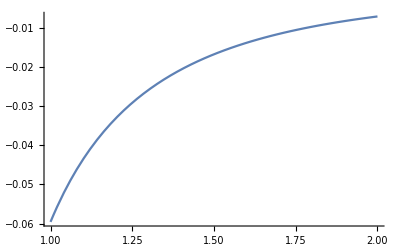

```mathematica
Plot[%/.n->-1, {tz, 1,2}]
```

```mathematica
exportContrib[expression_, outfile_, llist_]:=Module[{exportTo=outfile,tzinterval, expr=expression, exportTab},
tzinterval=Exp[Subdivide[Log[1.01],Log[2],50]];
exportTab=Table[
Table[expr, {tz,tzinterval}],
{n, llist}
];
exportTab=Prepend[exportTab, tzinterval];
exportTab=Prepend[Transpose[exportTab], "tz,"<>StringTake[ToString[-Range[3]], {2,-2}]];
Export[exportTo, exportTab, "TextDelimiters"->None]
]
exportContrib[expression_, outfile_]:=exportContrib[expression, outfile, -Range[3]] (* Note the minus sign *)
```

```mathematica
exportContrib[expr=1/(8 √((-1+n) n) (-1+tz^2))(n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))+2 n (-1+tz^2) √((-1+n) (1+(-1+n) tz^2))+n (6-6 tz^2) √(n (-1+n tz^2))+2 (-1+tz^2) √(n (-1+n tz^2))+4 n^2 (-1+tz^2) √(n (-1+n tz^2))-tz AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-2 √((-1+n) n) (-1+tz^2) (1+tz Log[1-n]-tz Log[(1+tz) √((1-n)/(-1+tz^2))]-tz Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))])+2 n √((-1+n) n) (2+tz-2 tz^2-tz^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(-1+n-√((-1+n) (-1+n tz^2)))/(n+n √((1+(-1+n) tz^2)/n))]), "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii.csv"]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii.csv

```mathematica
exportContrib[%52, "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_diffsigntz.csv"]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_diffsigntz.csv

```mathematica
"f"<>StringTake[ToString[-Range[3]], {2,-2}]
```

f-1, -2, -3

```mathematica
Export["/home/thorvald/Downloads/tmp/tst.csv", %%//Transpose]
```

/home/thorvald/Downloads/tmp/tst.csv

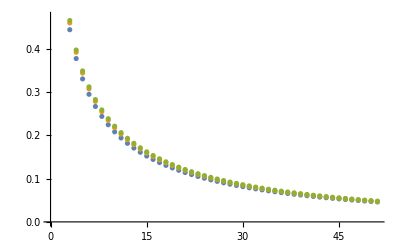

```mathematica
ListPlot[%]
```

```mathematica
Simplify[%119/.tz->-Abs[tz],{tz∈Reals, n∈NegativeIntegers}]
Simplify[%125/.tz->Abs[tz],{tz∈Reals, n∈NegativeIntegers}]
```

1/(8 √((-1+n) n) (-1+tz^2))(n^2 (4-4 tz^2) √((-1+n) (1+(-1+n) tz^2))-2 (-1+n) (-1+tz^2) √(n (-1+n tz^2))+4 (-1+n) n (-1+tz^2) √(n (-1+n tz^2))-2 n √((-1+n) (1+(-1+n) tz^2)) (1+Abs[tz])+2 n √((-1+n) (1+(-1+n) tz^2)) Abs[tz] (1+Abs[tz])-n Abs[tz] (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-Abs[tz] AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]-4 n^2 √((-1+n) n) (-1+tz^2) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]+2 n √((-1+n) n) (2-2 tz^2-Abs[tz]+Abs[tz]^3) Log[(√(n/(-1+n)) (√-n+√(-1+tz^2-n tz^2)))/(√(1-n)+√(1-n tz^2))]+2 √((-1+n) n) (-1+tz^2) (1+Abs[tz] (Log[1-n]-Log[(√-n+√(-1+tz^2-n tz^2))/(√(-1+tz^2))]-Log[√((1-n)/(-1+tz^2)) (1+Abs[tz])])))

```mathematica
FullSimplify[(%125/.tz->Abs[tz])+(%119/.tz->-Abs[tz]),{tz∈Reals, n∈NegativeIntegers}]
```

$Aborted

```mathematica
TeXForm[%]
```

\frac{| \text{tz}|  \left((n-1) F_1\left(1;\frac{1}{2},\frac{1}{2};2;\frac{1-n}{n
   \left(\text{tz}^2-1\right)},\frac{1}{1-\text{tz}^2}\right)-n
   F_1\left(1;\frac{1}{2},\frac{1}{2};2;\frac{1}{1-\text{tz}^2},-\frac{n}{(n-1)
   \left(\text{tz}^2-1\right)}\right)\right)+2 \left(\text{tz}^2-1\right) \left(-2 n^2 \sqrt{(n-1)
   \left((n-1) \text{tz}^2+1\right)}+2 n^2 \sqrt{n \left(n \text{tz}^2-1\right)}-\sqrt{(n-1) n} n^2
   \log \left(\frac{\sqrt{\frac{n-1}{n}} \left(\sqrt{1-n \text{tz}^2}+\sqrt{1-n}\right)}{\sqrt{-n
   \text{tz}^2+\text{tz}^2-1}+\sqrt{-n}}\right)-\sqrt{(n-1) n} n^2 \log \left(\frac{-\sqrt{(n-1)
   \left(n \text{tz}^2-1\right)}+n-1}{n \sqrt{\frac{(n-1) \text{tz}^2+1}{n}}+n}\right)+n
   \sqrt{(n-1) \left((n-1) \text{tz}^2+1\right)}-3 n \sqrt{n \left(n \text{tz}^2-1\right)}+\sqrt{n
   \left(n \text{tz}^2-1\right)}-2 \sqrt{(n-1) n} n \log \left(\frac{\sqrt{\frac{n}{n-1}}
   \left(\sqrt{-n \text{tz}^2+\text{tz}^2-1}+\sqrt{-n}\right)}{\sqrt{1-n
   \text{tz}^2}+\sqrt{1-n}}\right)\right)}{4 \sqrt{(n-1) n} \left(\text{tz}^2-1\right)}

```mathematica
FullSimplify[%138/.tz->-Abs[tz],{tz∈Reals, n∈NegativeIntegers}]
FullSimplify[%139/.tz->Abs[tz],{tz∈Reals, n∈NegativeIntegers}]
```

1/(8 √((-1+n) n) (-1+tz^2))(-4 n^2 (-1+tz^2) √(-1+n+(-1+n)^2 tz^2)-2 (-1+n) (-1+tz^2) √(n (-1+n tz^2))+4 (-1+n) n (-1+tz^2) √(n (-1+n tz^2))-2 n √(-1+n+(-1+n)^2 tz^2) (1+Abs[tz])+2 n √(-1+n+(-1+n)^2 tz^2) Abs[tz] (1+Abs[tz])-Abs[tz] AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)]+n Abs[tz] (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((-1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1-n)/(n (-1+tz^2)),1/(1-tz^2)])-4 n^2 √((-1+n) n) (-1+tz^2) Log[(√((-1+n)/n) (√(1-n)+√(1-n tz^2)))/(√-n+√(-1+tz^2-n tz^2))]+2 n √((-1+n) n) (2-2 tz^2-Abs[tz]+Abs[tz]^3) Log[(-n+√(n+(-1+n) n tz^2))/(1-n+√((-1+n) (-1+n tz^2)))]+√((-1+n) n) (-1+tz^2) (2+Abs[tz] (Log[1-n]-Log[1/(-1+tz^2)]-2 Log[((√-n+√(-1+tz^2-n tz^2)) (1+Abs[tz]))/(√(-1+tz^2))])))

$Aborted

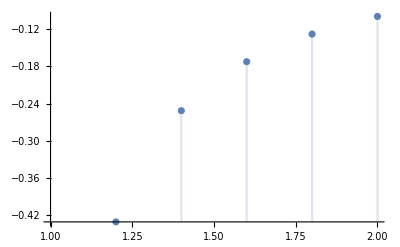

```mathematica
DiscretePlot[
{%151}/.n->-1
, {tz, 1,2,0.2}]
```

```mathematica
%129/.n->-1//Simplify
```

1/(8 √2 (-1+Abs[tz]^2))(12 (-1+Abs[tz]^2) √(1+Abs[tz]^2)-6 (-1+Abs[tz]^2) √(-2+4 Abs[tz]^2)+Abs[tz] (AppellF1[1,1/2,1/2,2,1/(1-Abs[tz]^2),1/(2-2 Abs[tz]^2)]-AppellF1[1,1/2,1/2,2,-2/(-1+Abs[tz]^2),1/(1-Abs[tz]^2)])-Abs[tz] AppellF1[1,1/2,1/2,2,-2/(-1+Abs[tz]^2),1/(1-Abs[tz]^2)]-4 √2 (-1+Abs[tz]^2) Log[(2+√2 √(1+Abs[tz]^2))/(1+√(-1+2 Abs[tz]^2))]+2 √2 (-1+Abs[tz]^2) (-1+Abs[tz] (Log[((1+Abs[tz]) √(1/(-1+Abs[tz]^2)))/(√2)]+Log[(1+√(-1+2 Abs[tz]^2))/(√(-1+Abs[tz]^2))]))+2 √2 (-2-Abs[tz]+2 Abs[tz]^2+Abs[tz]^3) Log[(1+√(-1+2 Abs[tz]^2))/(2+√2 √(1+Abs[tz]^2))])

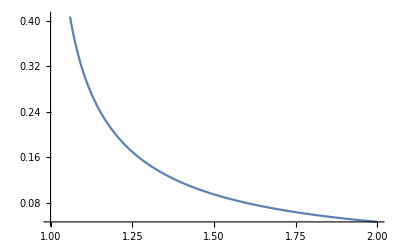

```mathematica
Plot[%, {tz, 1,2}]
```

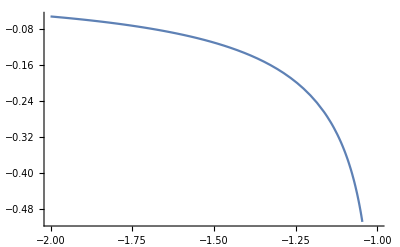

```mathematica
Plot[%128/.n->-1//Simplify, {tz, -2,-1}]
```

```mathematica
Simplify[%74/.n->-1, extraAssumptions]
```

1/(16 (-1+tz^2))(4-12 tz-12 √2 √(1+tz^2)+4 √2 tz √(1+tz^2)+12 √(-1+2 tz^2)-4 tz √(-1+2 tz^2)+4 (3-√2 √(1+tz^2)+√(-1+2 tz^2)+tz (-1+3 √2 √(1+tz^2)-3 √(-1+2 tz^2))) Abs[tz]+√2 tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 √2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+Log[16]-tz Log[16]-tz^2 Log[16]-tz^3 Log[16]+tz Log[256]+4 tz Log[-1+tz^2]-4 tz^3 Log[-1+tz^2]+8 Log[√2+√(1+tz^2)]+4 tz Log[√2+√(1+tz^2)]-8 tz^2 Log[√2+√(1+tz^2)]-4 tz^3 Log[√2+√(1+tz^2)]+8 Log[2+√2 √(1+tz^2)]-8 tz^2 Log[2+√2 √(1+tz^2)]-16 Log[1+√(-1+2 tz^2)]-8 tz Log[1+√(-1+2 tz^2)]+16 tz^2 Log[1+√(-1+2 tz^2)]+8 tz^3 Log[1+√(-1+2 tz^2)]-4 tz Log[1+Abs[tz]]+4 tz^3 Log[1+Abs[tz]])

```mathematica
tzpos=Refine[1/(16 (-1+tz^2))(4-12 tz-12 √2 √(1+tz^2)+4 √2 tz √(1+tz^2)+12 √(-1+2 tz^2)-4 tz √(-1+2 tz^2)+4 (3-√2 √(1+tz^2)+√(-1+2 tz^2)+tz (-1+3 √2 √(1+tz^2)-3 √(-1+2 tz^2))) Abs[tz]+√2 tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 √2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+Log[16]-tz Log[16]-tz^2 Log[16]-tz^3 Log[16]+tz Log[256]+4 tz Log[-1+tz^2]-4 tz^3 Log[-1+tz^2]+8 Log[√2+√(1+tz^2)]+4 tz Log[√2+√(1+tz^2)]-8 tz^2 Log[√2+√(1+tz^2)]-4 tz^3 Log[√2+√(1+tz^2)]+8 Log[2+√2 √(1+tz^2)]-8 tz^2 Log[2+√2 √(1+tz^2)]-16 Log[1+√(-1+2 tz^2)]-8 tz Log[1+√(-1+2 tz^2)]+16 tz^2 Log[1+√(-1+2 tz^2)]+8 tz^3 Log[1+√(-1+2 tz^2)]-4 tz Log[1+Abs[tz]]+4 tz^3 Log[1+Abs[tz]]), tz>1]
```

1/(16 (-1+tz^2))(4-12 tz-12 √2 √(1+tz^2)+4 √2 tz √(1+tz^2)+12 √(-1+2 tz^2)-4 tz √(-1+2 tz^2)+4 tz (3-√2 √(1+tz^2)+√(-1+2 tz^2)+tz (-1+3 √2 √(1+tz^2)-3 √(-1+2 tz^2)))+√2 tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 √2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+Log[16]-tz Log[16]-tz^2 Log[16]-tz^3 Log[16]+tz Log[256]-4 tz Log[1+tz]+4 tz^3 Log[1+tz]+4 tz Log[-1+tz^2]-4 tz^3 Log[-1+tz^2]+8 Log[√2+√(1+tz^2)]+4 tz Log[√2+√(1+tz^2)]-8 tz^2 Log[√2+√(1+tz^2)]-4 tz^3 Log[√2+√(1+tz^2)]+8 Log[2+√2 √(1+tz^2)]-8 tz^2 Log[2+√2 √(1+tz^2)]-16 Log[1+√(-1+2 tz^2)]-8 tz Log[1+√(-1+2 tz^2)]+16 tz^2 Log[1+√(-1+2 tz^2)]+8 tz^3 Log[1+√(-1+2 tz^2)])

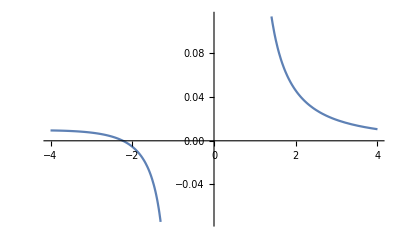

```mathematica
Plot[%7/.tz->x, x ∈ImplicitRegion[-4<x<-1 ∨4>x>1, {x}]]
```

```mathematica
Simplify[%74+(%74/.tz->-tz)/.n->-1, extraAssumptions]
```

1/(2 (-1+tz^2))(1-3 √2 √(1+tz^2)+3 √(-1+2 tz^2)+(3-√2 √(1+tz^2)+√(-1+2 tz^2)) Abs[tz]+Log[2]+tz^2 Log[2]-tz^2 Log[4]-2 (-1+tz^2) Log[√2+√(1+tz^2)]+2 Log[2+√2 √(1+tz^2)]-2 tz^2 Log[2+√2 √(1+tz^2)]-4 Log[1+√(-1+2 tz^2)]+4 tz^2 Log[1+√(-1+2 tz^2)])

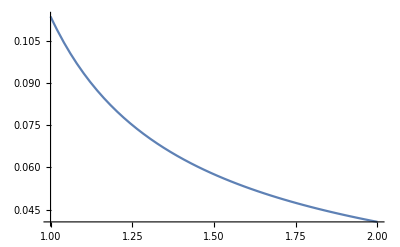

```mathematica
Plot[%, {tz, 1,2}]
```

```mathematica
FullSimplify[%, extraAssumptions]
```

$Aborted

```mathematica
FullSimplify[%20/.n->-1, assumptions]
```

1/(8 √2 (-1+tz^2))(tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+(-1+tz^2) (-2 √2+12 √(1+tz^2)-6 √(-2+4 tz^2)-2 √2 (Log[2]+tz Log[2 (-1+tz) (√2+√(1+tz^2))]+2 Log[3 √2+√2 tz^2+4 √(1+tz^2)]-2 (2+tz) Log[1+√(-1+2 tz^2)])))

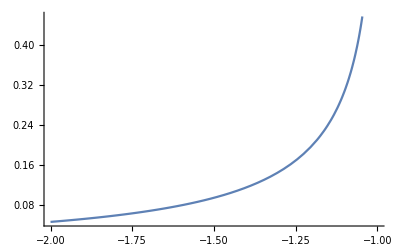

```mathematica
Plot[Evaluate[1/(8 √2 (-1+tz^2))(tz AppellF1[1,1/2,1/2,2,1/(1-tz^2),1/(2-2 tz^2)]-2 tz AppellF1[1,1/2,1/2,2,-2/(-1+tz^2),1/(1-tz^2)]+(-1+tz^2) (-2 √2+12 √(1+tz^2)-6 √(-2+4 tz^2)-2 √2 (Log[2]+tz Log[2 (-1+tz) (√2+√(1+tz^2))]+2 Log[3 √2+√2 tz^2+4 √(1+tz^2)]-2 (2+tz) Log[1+√(-1+2 tz^2)])))/.tz->Abs[tz]], {tz,-2,-1}]
```

General m>0, n>0, remember M-1=N

```mathematica
extraAssumptions2={n>0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz>1,-1+m==n}
```

{n>0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz>1,-1+m==n}

```mathematica
integrand=Refine[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2,
extraAssumptions2
]
```

(m (√(kappa^2+m)+√(kappa^2+n)+2 kappa tz))/((√(kappa^2+m)-√(kappa^2+n))^2 (-kappa+√(kappa^2+m) s)^2 (1+m/((-kappa+√(kappa^2+m) s)^2)) (1+n/((-kappa+√(kappa^2+n) s)^2)))

```mathematica
Simplify[integrand/.s->1/.m->n+1, extraAssumptions2]
```

((1+n) (kappa-√(kappa^2+n))^2 (√(kappa^2+n)+√(1+kappa^2+n)+2 kappa tz))/(4 (kappa^2+n-kappa √(kappa^2+n)) (√(kappa^2+n)-√(1+kappa^2+n))^2 (1+kappa^2+n-kappa √(1+kappa^2+n)))

```mathematica
Integrate[%, {kappa, -Sqrt[m/(tz^2-1)]/.m->n+1, -Sqrt[n/(tz^2-1)]}, Assumptions->extraAssumptions2]
```

1/(8 √n √(1+n) (-1+tz^2))(-2 (1+n) (-1+tz^2) √(n (1+n tz^2))-4 n (1+n) (-1+tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])+2 √(n (1+n)) (-1+tz^2) (-1+tz Log[(1+tz) √((1+n)/(-1+tz^2))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])+2 n^(3/2) √(1+n) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]-4 n^(5/2) √(1+n) (-1+tz^2) Log[(n+√(n (-1+(1+n) tz^2)))/(1+n+√((1+n) (1+n tz^2)))])

```mathematica
intrabandtzpositive=1/(8 √n √(1+n) (-1+tz^2))(-2 (1+n) (-1+tz^2) √(n (1+n tz^2))-4 n (1+n) (-1+tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])+2 √(n (1+n)) (-1+tz^2) (-1+tz Log[(1+tz) √((1+n)/(-1+tz^2))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])+2 n^(3/2) √(1+n) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]-4 n^(5/2) √(1+n) (-1+tz^2) Log[(n+√(n (-1+(1+n) tz^2)))/(1+n+√((1+n) (1+n tz^2)))])
```

1/(8 √n √(1+n) (-1+tz^2))(-2 (1+n) (-1+tz^2) √(n (1+n tz^2))-4 n (1+n) (-1+tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+n tz (-AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]+AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])+2 √(n (1+n)) (-1+tz^2) (-1+tz Log[(1+tz) √((1+n)/(-1+tz^2))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])+2 n^(3/2) √(1+n) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]-4 n^(5/2) √(1+n) (-1+tz^2) Log[(n+√(n (-1+(1+n) tz^2)))/(1+n+√((1+n) (1+n tz^2)))])

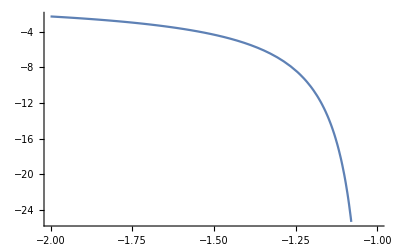

```mathematica
Plot[intrabandtznegative/.n->1, {tz,-2,-1}]
```

```mathematica
exportContrib[intrabandtzpositive, "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband.csv", Range[3]]
exportContrib[intrabandtzpositive + (intrabandtznegative/.tz->-tz), "/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband_diffsigntz.csv",Range[3]]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/contribtypeii_intraband_diffsign.csv

```mathematica
extraAssumptions2={n>0,m>0,s^2==1,(n|m|s)∈Integers,(kappa|tz)∈Reals,tz<-1,-1+m==n}
```

{n>0,m>0,s^2==1,(n|m|s)∈ℤ,(kappa|tz)∈ℝ,tz<-1,-1+m==n}

```mathematica
integrand=Refine[
xi ((ϵ0[m] + ϵ0[n]) + 2 ϵdiv) alpha[m]^2,
extraAssumptions2
]
```

(m (√(kappa^2+m)+√(kappa^2+n)+2 kappa tz))/((√(kappa^2+m)-√(kappa^2+n))^2 (-kappa+√(kappa^2+m) s)^2 (1+m/((-kappa+√(kappa^2+m) s)^2)) (1+n/((-kappa+√(kappa^2+n) s)^2)))

```mathematica
Simplify[integrand/.s->1/.m->n+1, extraAssumptions2]
```

((1+n) (kappa-√(kappa^2+n))^2 (√(kappa^2+n)+√(1+kappa^2+n)+2 kappa tz))/(4 (kappa^2+n-kappa √(kappa^2+n)) (√(kappa^2+n)-√(1+kappa^2+n))^2 (1+kappa^2+n-kappa √(1+kappa^2+n)))

```mathematica
Integrate[%, {kappa, Sqrt[n/(tz^2-1)], Sqrt[m/(tz^2-1)]/.m->n+1}, Assumptions->extraAssumptions2]
```

1/(8 √(n (1+n)) (-1+tz^2))(n (6-6 tz^2) √(n (1+n tz^2))+n^2 (4-4 tz^2) √(n (1+n tz^2))+(2-2 tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])-tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+2 √(n (1+n)) (-1+tz^2) (1+tz Log[-((-1+tz) √((1+n)/(-1+tz^2)))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])-4 n^2 √(n (1+n)) (-1+tz^2) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]+2 n √(n (1+n)) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))])

```mathematica
intrabandtznegative=1/(8 √(n (1+n)) (-1+tz^2))(n (6-6 tz^2) √(n (1+n tz^2))+n^2 (4-4 tz^2) √(n (1+n tz^2))+(2-2 tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])-tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+2 √(n (1+n)) (-1+tz^2) (1+tz Log[-((-1+tz) √((1+n)/(-1+tz^2)))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])-4 n^2 √(n (1+n)) (-1+tz^2) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]+2 n √(n (1+n)) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))])
```

1/(8 √(n (1+n)) (-1+tz^2))(n (6-6 tz^2) √(n (1+n tz^2))+n^2 (4-4 tz^2) √(n (1+n tz^2))+(2-2 tz^2) √(n (1+n tz^2))+2 n (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+4 n^2 (-1+tz^2) √((1+n) (-1+(1+n) tz^2))+n tz (AppellF1[1,1/2,1/2,2,1/(1-tz^2),-n/((1+n) (-1+tz^2))]-AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)])-tz AppellF1[1,1/2,1/2,2,(1+n)/(n-n tz^2),1/(1-tz^2)]+2 √(n (1+n)) (-1+tz^2) (1+tz Log[-((-1+tz) √((1+n)/(-1+tz^2)))]-tz Log[(√n+√(-1+(1+n) tz^2))/(√(-1+tz^2))])-4 n^2 √(n (1+n)) (-1+tz^2) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))]+2 n √(n (1+n)) (2+tz-2 tz^2-tz^3) Log[(√(n/(1+n)) (√n+√(-1+(1+n) tz^2)))/(√(1+n)+√(1+n tz^2))])